## Style

```mathematica
dir=NotebookDirectory[]

"/home/nicolas/git/talks/Oléron 2016/img/"

(*Thickness*)
th=0.003;

(*Styling of the text*)

st=Directive[FontSize->15,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];

BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];

SetOptions[ListPlot,Frame->False,FrameStyle->st,PlotRange->All];
```

/home/nicolas/git/talks/Bratislava november 2016/img/

/home/nicolas/git/talks/Oléron 2016/img/

## Utility functions

```mathematica
(* string substitution *)
Sub[rule_,init_String,l_Integer]:=Nest[StringReplace[#,rule]&,init,l]
```

```mathematica
(* Height (integrated arrow field), can also be seen as the mode k=0 of the Fourier transform of the sequence of arrows *)
Heights[arrows_]:=Table[Total[arrows[[;;N]]],{N,1,Length[arrows]}];
```

```mathematica
(* maximum of the height distribution *)
MaxHeights[heights_]:=Block[{absheights=Abs[heights]},Table[Max[absheights[[;;N]]],{N,1,Length[heights]}]];
```

```mathematica
(* for a string of an even number of A and B, replace every couple by the corresponding arrow *)
ToArrowAlphabet[string_]:=StringReplace[string,{"AB"->"R","BA"->"L","AA"->"Ia","BB"->"Ib"}];
(* return the vector counting the number of arrows *)
ArrowCountVec[string_]:=StringCount[string,#]&/@{"R","L","Ia","Ib"};
```

```mathematica
(* periodic approximant of a sequence seq of two letters, in normal numbering *)
h[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];
(* boundary conditions for the nearest neighbour hoppings *)
PrependTo[tbl,{1,n}->jump[n]];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

For the E=0 level to exist, we need an odd number of letters. But we also need the system to be bipartite for the wavefunction to be nonzero only on one site over two → open boundary conditions.

```mathematica
(* open approximant of a sequence seq of two letters, in normal numbering *)
ho[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

## Fibonacci substitution

```mathematica
(* inflation matrix on the arrows of the Fibonacci chain *)
M={{2,1,2},{1,2,2},{1,1,1}};
```

```mathematica
Eigensystem[M]
```

{{2+√5,1,2-√5},{{1/2 (1+√5),1/2 (1+√5),1},{-1,1,0},{1/2 (1-√5),1/2 (1-√5),1}}}

```mathematica
(* whithout surprise the largest eigenvalue is τ^3 *)
((1+√5)/2)^3//Expand
```

2+√5

```mathematica
(* Fibonacci substitution *)
FiboSub[l_,C0_String]:=Sub[{"A"->"AB","B"->"A"},C0,l];
(* Fibonacci substitution, composed 3 times *)
FiboSub3[l_,C0_String]:=Sub[{"A"->"ABABA","B"->"ABA"},C0,l];
ArrowSub[l_,C0_String]:=Sub[{"R"->"RILL","L"->"RILR","I"->"RILLR"},C0,l];
FiboArrows2[string_]:=StringPartition[string,1]/.{"R"->1,"L"->-1,"I"->0};
LocalEnvs={"RR","RI","LL","IL","LR"};
HeightCount[ArrowString_]:=StringCount[ArrowString,#]&/@LocalEnvs;
LocalEnvs2={"R","L","I"};
HeightCount2[ArrowString_]:=StringCount[ArrowString,#]&/@LocalEnvs2;
(* the field of arrows *)
FiboArrows[l_]:=StringPartition[FiboSub3[l,"AB"],2]/.{"AB"->1,"BA"->-1,"AA"->0};
```

### Numerical study of the heights

```mathematica
ToArrowAlphabet@FiboSub3[1,#]&/@{"AB","BA","AA","BB"}
```

{RRIaL,RIaLL,RRIaLL,RIaL}

```mathematica
ToArrowAlphabet@FiboSub[3,#]&/@{"AB","BA","AA","BB"}
```

{RIaLL,RIaLR,RIaLLR,RIaL}

```mathematica
(* inflation matrix *)
FiboM=ArrowCountVec@ToArrowAlphabet@FiboSub[3,#]&/@{"AB","BA","AA","BB"};
FiboM=Transpose[FiboM];
FiboM//MatrixForm
(* the "BB"="Ib" sequence is not allowed, so we can drop the last line and columns of the matrix*)
FiboM=FiboM[[;;3,;;3]];
FiboM//MatrixForm
```

(1 | 2 | 2 | 1
2 | 1 | 2 | 1
1 | 1 | 1 | 1
0 | 0 | 0 | 0)

(1 | 2 | 2
2 | 1 | 2
1 | 1 | 1)

```mathematica
{sp,vecs}=Eigensystem[FiboM]
(* change of basis matrix *)
P=Transpose[vecs];
PI=Inverse[P]//Simplify;
```

{{2+√5,-1,2-√5},{{(2 (2+√5))/(3+√5),(2 (2+√5))/(3+√5),1},{-1,1,0},{(2 (-2+√5))/(-3+√5),(2 (-2+√5))/(-3+√5),1}}}

```mathematica
PI//MatrixForm
```

(1/(2 √5) | 1/(2 √5) | 1/10 (5-√5)
-1/2 | 1/2 | 0
-1/(2 √5) | -1/(2 √5) | 1/10 (5+√5))

```mathematica
PI.FiboM.P//Simplify//MatrixForm
```

(2+√5 | 0 | 0
0 | -1 | 0
0 | 0 | 2-√5)

```mathematica
arrows=FiboArrows[7];
FiboHeights=Heights[arrows];
```

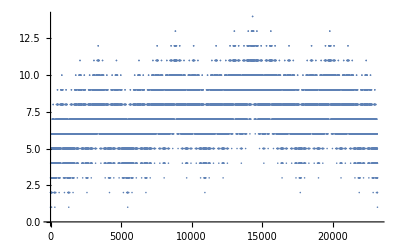

```mathematica
(* the height max grows logarithmically, and the height function goes to 0 arbitrarily far from the origin *)
ListPlot[FiboHeights]
```

```mathematica
FiboMaxs=MaxHeights[FiboHeights];
```

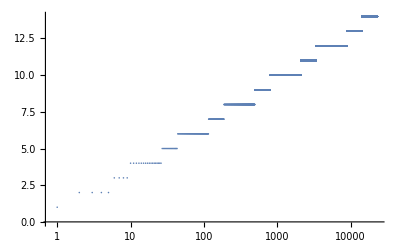

```mathematica
(* the height max grows logarithmically! *)
ListLogLinearPlot[FiboMaxs,PlotRange->All]
```

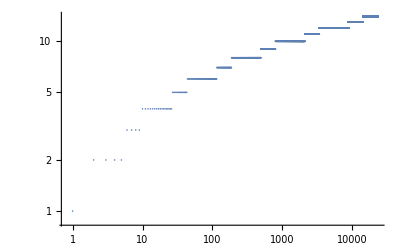

```mathematica
(* the height max doesn't grow like a power-law *)
ListLogLogPlot[FiboMaxs,PlotRange->All]
```

### Generalized inflation matrix

```mathematica
(* First we work with first neighbors local environments *)
LocalEnvs
```

{RL,LI,IR,II}

```mathematica
(* we obtain the inflation matrix for these environments straightforwardly by counting them *)
A=HeightCount/@(ArrowSub[1,#]&/@LocalEnvs);
Transpose[A]//MatrixForm
```

(0 | 0 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2
2 | 2 | 0 | 1 | 1
2 | 2 | 2 | 2 | 2
1 | 2 | 2 | 2 | 1)

```mathematica
(* but weirdly, the matrix has eigenvalues in a different algebraic field *)
Eigensystem[Transpose[A]]
```

{{1/2 (7+√65),-1,-1,1/2 (7-√65),0},{{-(-201-25 √65)/(5 (105+13 √65)),(4 (2959+367 √65))/(5 (11+√65) (105+13 √65)),(4 (1765+219 √65))/(5 (11+√65) (105+13 √65)),-(-621-77 √65)/(5 (105+13 √65)),1},{0,0,-1,0,1},{0,0,0,0,0},{-(201-25 √65)/(5 (-105+13 √65)),-(4 (-2959+367 √65))/(5 (-11+√65) (-105+13 √65)),-(4 (-1765+219 √65))/(5 (-11+√65) (-105+13 √65)),-(621-77 √65)/(5 (-105+13 √65)),1},{-1,1,0,-1,1}}}

```mathematica
(* secondly, we look at local environments defined by "the letter at the right of the current site" *)
LocalEnvs2
```

{R,L,I}

```mathematica
(* the inflation matrix this time has eigenvalues in the expected field *)
A=HeightCount2/@(ArrowSub[1,#]&/@LocalEnvs2);
Transpose[A]//MatrixForm
Eigensystem[Transpose[A]]
```

(1 | 2 | 2
2 | 1 | 2
1 | 1 | 1)

{{2+√5,-1,2-√5},{{(2 (2+√5))/(3+√5),(2 (2+√5))/(3+√5),1},{-1,1,0},{(2 (-2+√5))/(-3+√5),(2 (-2+√5))/(-3+√5),1}}}

```mathematica
(* a dictionary from envs to indices *)
envs={"R","L","I"};
Idx=<|"R"->1,"L"->2,"I"->3|>;
inflatedEnvs=ArrowSub[1,#]&/@envs;
inflatedArrows=({0}~Join~FiboArrows2[#][[;;-2]])&/@inflatedEnvs;
inflatedHeights=Table[Total[#[[;;L]]],{L,1,Length[#]}]&/@inflatedArrows;
RowsHeights=MapThread[{#1,#2}&,{inflatedEnvs,inflatedHeights}];
(* construct the matrices *)
table0=Table[0,{i,1,3},{j,1,3}];
T2left=table0;
T20=table0;
T2right=table0;
(* a way of constructing the generalized matrices automatically *)
For[col=1,col≤3,col++,
{rows,heights}=RowsHeights[[col]];
rows=StringPartition[rows,1];
For[i=1,i≤Length[rows],i++,
h=heights[[i]];
row=Idx[rows[[i]]];
If[h==-1,
T2left[[row,col]]+=1,
If[h==0,
T20[[row,col]]+=1,
If[h==1,
T2right[[row,col]]+=1]]]
]
]
```

```mathematica
T2left==Tleft
T2right==Tright
T20==T0
```

True

True

True

```mathematica
(* generalized inflation matrices for height dependent environments *)
T0={{1,2,1},{1,0,1},{0,0,0}};
Tright={{0,0,0},{1,1,1},{1,1,1}};
Tleft={{0,0,1},{0,0,0},{0,0,0}};
(* generating function of the height distribution *)
T[β_]:=β^-1 Tleft+T0+β Tright
```

```mathematica
Eigensystem[T[β]]
```

{{-1,(β+β^2-√(β^2 (2+2 β+β^2)))/β,(β+β^2+√(β^2 (2+2 β+β^2)))/β},{{-1,1,0},{(3 β+β^2-2 √(β^2 (2+2 β+β^2)))/(β (2 β+β^2-√(β^2 (2+2 β+β^2)))),(β+2 β^2+β^3-√(β^2 (2+2 β+β^2))-β √(β^2 (2+2 β+β^2)))/(β (2 β+β^2-√(β^2 (2+2 β+β^2)))),1},{-(-3 β-β^2-2 √(β^2 (2+2 β+β^2)))/(β (2 β+β^2+√(β^2 (2+2 β+β^2)))),-(-β-2 β^2-β^3-√(β^2 (2+2 β+β^2))-β √(β^2 (2+2 β+β^2)))/(β (2 β+β^2+√(β^2 (2+2 β+β^2)))),1}}}

```mathematica
(* Perron-Froebenius eigenvalue *)
ω[β_]:=1+β+√(2+2 β+β^2)
(* Perron-Froebenius eigenvector of T[β] *)
f[β_]:={1/2 (β+2 β^2+(1-2β)√(2+β (2+β))),1/2 (2+β-√(2+β (2+β))),β (-1-β+√(2+β (2+β)))}
```

The average height is <h_μ> = lim_(t→∞) (d log ω^t(β)f_μ(β))/(d log β)|_(β=1)
If ω'(1)=0, the average height is well defined in the QP limit. Otherwise there is a drift that is linear in the number of inflations.

```mathematica
(* here the is a nonzero drift of the average values! *)
D[ω[Exp[tt]],tt]/.tt->0
drift=%/ω[1]//Simplify
```

1+2/(√5)

1/(√5)

```mathematica
(* average without the drift term *)
average=D[Log[f[Exp[tt]]],tt]/.tt->0//FullSimplify
%-Last[%]//N
```

{3/4-11/(4 √5),1/20 (5-√5),1-1/(√5)}

{-1.03262,-0.41459,0.}

```mathematica
(* variance *)
var=D[Log[ω[Exp[tt]]],{tt,2}]/.tt->0//FullSimplify
%//N
```

3/(5 √5)

0.268328

```mathematica
f[1]
```

{1/2 (3-√5),1/2 (3-√5),-2+√5}

```mathematica
(* numerical check! *)
t=9;
word=ArrowSub[t,"R"];
arrows={0}~Join~FiboArrows2[word][[;;-2]];
heights=Heights[arrows];
HeightOnLocalEnvs=MapThread[ {#1,#2}&,{StringPartition[word,1],heights}];
SortedHeightsOnLocalEnvs=Gather[HeightOnLocalEnvs,First[#1]==First[#2]&];
Averages=N@Mean[Transpose[#][[2]]]&/@SortedHeightsOnLocalEnvs
Averages-Last[Averages]
```

{-0.190982,1.11803,0.809013}

{-0.999995,0.309021,0.}

```mathematica
StringLength[word]
```

416020

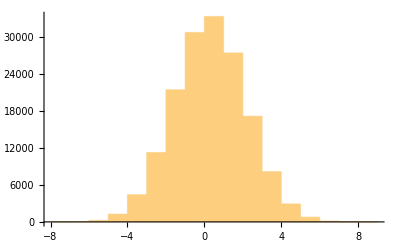

```mathematica
dataR=Transpose[SortedHeightsOnLocalEnvs[[1]]][[2]];
dataL=Transpose[SortedHeightsOnLocalEnvs[[2]]][[2]];
dataI=Transpose[SortedHeightsOnLocalEnvs[[3]]][[2]];
Histogram[dataR]
```

```mathematica
𝒟R=HistogramDistribution[dataR];
𝒟L=HistogramDistribution[dataL];
𝒟I=HistogramDistribution[dataI];
```

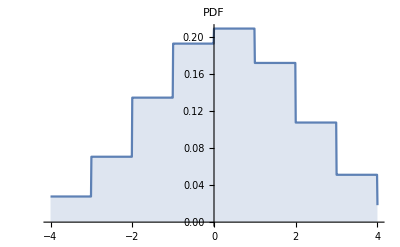
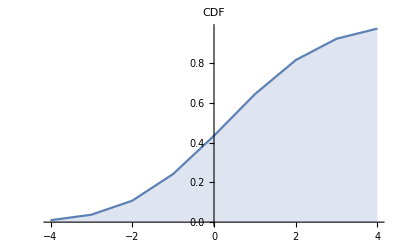

```mathematica
DiscretePlot[#[𝒟R,x],{x,-4,4,.01},PlotLabel->#]&/@{PDF,CDF}
```

```mathematica
totalDrift=t*drift;
Moment[#,1]&/@{𝒟R,𝒟L,𝒟I}//N
%-drift
%-Last[%]
```

{0.309018,1.61803,1.30901}

{-0.138196,1.17082,0.861799}

{-0.999995,0.309021,0.}

```mathematica
drift
```

9 (1+2/(√5))

```mathematica
Moment[𝒟I,2]//N
%/(t)
```

5.35267

0.594741

## Ag substitution

```mathematica
AgSub[l_,C0_String]:=Sub[{"A"->"AAB","B"->"A"},C0,l];
(* the field of arrows *)
AgArrows[l_]:=StringPartition[AgSub[l,"AB"],2]/.{"AB"->1,"BA"->-1,"AA"->0,"BB"->0};
```

```mathematica
(* we have to iterate only 1 time to obtain an effective substitution acting on the arrows *)
n=1;
AgSub[n,"B"]
StringLength[%]
AgSub[n,"A"]
StringLength[%]
```

A

1

AAB

3

```mathematica
(* inflation matrix *)
AgM=ArrowCountVec@ToArrowAlphabet@AgSub[1,#]&/@{"AB","BA","AA","BB"};
AgM=Transpose[AgM];
AgM//MatrixForm
(* the "BB" environment is forbidden, so we can drop it *)
AgM=AgM[[;;3,;;3]];
AgM//MatrixForm
```

(0 | 1 | 1 | 0
1 | 0 | 1 | 0
1 | 1 | 1 | 1
0 | 0 | 0 | 0)

(0 | 1 | 1
1 | 0 | 1
1 | 1 | 1)

```mathematica
(* the spectrum is like the Fibo one: the 2 algebraically conjugate numbers and -1 *)
Eigensystem[AgM]
```

{{1+√2,-1,1-√2},{{-(-1-√2)/(2+√2),-(-1-√2)/(2+√2),1},{-1,1,0},{-(1-√2)/(-2+√2),-(1-√2)/(-2+√2),1}}}

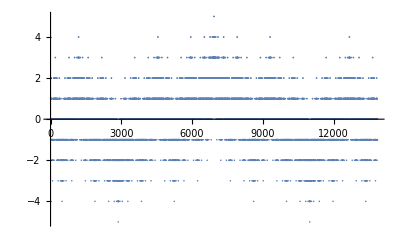

```mathematica
arrows=AgArrows[11];
AgHeights=Heights[arrows];
(* the height function goes to 0 arbitrarily far from the origin *)
ListPlot[AgHeights,PlotRange->All]
```

```mathematica
AgMaxs=MaxHeights[AgHeights];
```

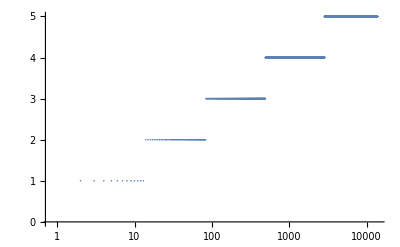

```mathematica
(* the height max grows logarithmically! *)
ListLogLinearPlot[AgMaxs,PlotRange->All]
```

```mathematica
mat=ho[ρ,AgSub[9,"B"]];
{vals,vecs}=Eigensystem[mat];
o=Ordering[vals];
vals=vals[[o]];
vecs=vecs[[o]];
```

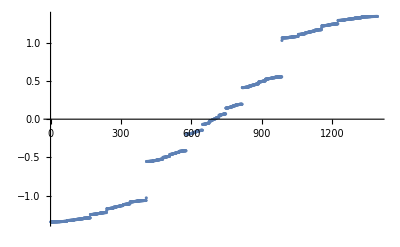

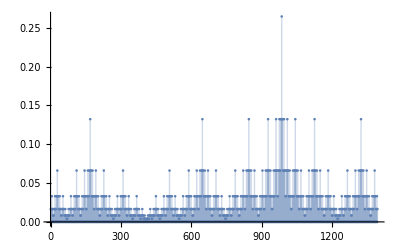

```mathematica
ListPlot[vals]
idxCenter=(Length[vals]+1)/2;
ListPlot[Abs@vecs[[idxCenter]],Filling->Axis,PlotRange->All]
```

## B2 substitution

```mathematica
B2Sub[l_,C0_String]:=Sub[{"A"->"ABB","B"->"A"},C0,l];
(* the field of arrows *)
B2Arrows[l_,C0_String]:=StringPartition[B2Sub[l,C0],2]/.{"AB"->1,"BA"->-1,"AA"->0,"BB"->0};
```

```mathematica
(* we have to iterate at just 1 time to obtain an effective substitution acting on the arrows! *)
n=1;
B2Sub[n,"B"]
StringLength[%]
B2Sub[n,"A"]
StringLength[%]
```

A

1

ABB

3

```mathematica
(* inflation matrix for the arrows *)
ToArrowAlphabet@B2Sub[1,"AB"]
ToArrowAlphabet@B2Sub[1,"BA"]
ToArrowAlphabet@B2Sub[1,"AA"]
ToArrowAlphabet@B2Sub[1,"BB"]
```

RL

IaIb

RLIb

Ia

```mathematica
(* inflation matrix *)
B2M=ArrowCountVec@ToArrowAlphabet@B2Sub[1,#]&/@{"AB","BA","AA","BB"};
B2M=Transpose[B2M];
B2M//MatrixForm
```

(1 | 0 | 1 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 1 | 1 | 0)

```mathematica
Eigensystem[B2M]
```

{{2,-1,0,0},{{1,1,1,1},{1,1,-2,1},{-1,-1,1,1},{0,0,0,0}}}

```mathematica
B2Arrows[5,"AB"]
```

{1,-1,0,0,1,-1,0,0,1,-1,0,0,0,1,-1,0,1,-1,0,0,1,-1,0,0,1,-1,0,1,-1,0,0,0}

```mathematica
arrows=B2Arrows[10,"AB"];
B2Heights=Heights[arrows];
```

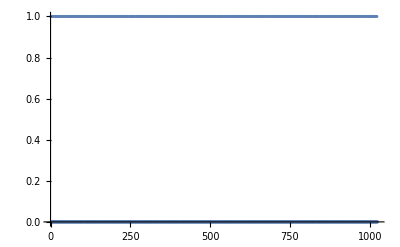

```mathematica
(* the height function goes to 0 arbitrarily far from the origin *)
ListPlot[B2Heights,PlotRange->All]
```

```mathematica
mat=ho[ρ,B2Sub[10,"B"]];
{vals,vecs}=Eigensystem[mat];
o=Ordering[vals];
vals=vals[[o]];
vecs=vecs[[o]];
```

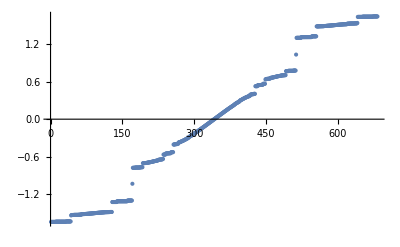

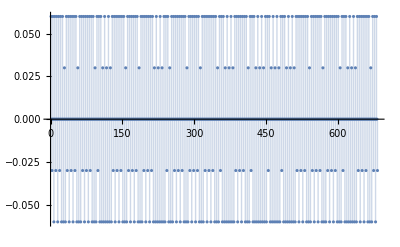

```mathematica
ListPlot[vals]
idxCenter=(Length[vals]+1)/2;
ListPlot[vecs[[idxCenter]],Filling->Axis,PlotRange->All]
```

## B3 substitution (simplest example of non-Pisot)

```mathematica
Mnp={{1,1},{3,0}};
```

```mathematica
Eigenvalues[Mnp]
%//N
```

{1/2 (1+√13),1/2 (1-√13)}

{2.30278,-1.30278}

```mathematica
(* B3 substitution *)
B3Sub[l_,C0_String]:=Sub[{"A"->"ABBB","B"->"A"},C0,l];
(* B3 substitution, composed 3 times *)
B3Sub3[l_,C0_String]:=Sub[{"A"->"ABBBAAAABBBABBBABBB","B"->"ABBBAAA"},C0,l];
(* the field of arrows *)
B3Arrows[l_]:=StringPartition[B3Sub3[l,"AB"],2]/.{"AB"->1,"BA"->-1,"AA"->0,"BB"->0};
B3ArrowSub[l_,C0_String]:=Sub[{"R"->"RbaabLbLbLbLa","L"->"RbaabLaRbRbRb","a"->"RbaabLbLbLbLaRbRbRb","b"->"RbaabLa"},C0,l];
B3Arrows2[string_]:=StringPartition[string,1]/.{"R"->1,"L"->-1,"a"->0,"b"->0};
```

### Behavior of the heights

```mathematica
(* we have to iterate at least 3 times to obtain an effective substitution acting on the arrows *)
n=3;
B3Sub[n,"B"]
StringLength[%]
B3Sub[n,"A"]
StringLength[%]
```

ABBBAAA

7

ABBBAAAABBBABBBABBB

19

```mathematica
(* inflation matrix for the arrows *)
ToArrowAlphabet@B3Sub3[1,"AB"]
ToArrowAlphabet@B3Sub3[1,"BA"]
ToArrowAlphabet@B3Sub3[1,"AA"]
ToArrowAlphabet@B3Sub3[1,"BB"]
```

RIbIaIaIbLIbLIbLIbLIa

RIbIaIaIbLIaRIbRIbRIb

RIbIaIaIbLIbLIbLIbLIaRIbRIbRIb

RIbIaIaIbLIa

```mathematica
(* inflation matrix *)
B3M=ArrowCountVec@ToArrowAlphabet@B3Sub3[1,#]&/@{"AB","BA","AA","BB"};
B3M=Transpose[B3M];
B3M//MatrixForm
```

(1 | 4 | 4 | 1
4 | 1 | 4 | 1
3 | 3 | 3 | 3
5 | 5 | 8 | 2)

```mathematica
((1-√13)/2)^3//Expand//FullSimplify
```

5-2 √13

```mathematica
B3subM={{1,1},{3,0}};
MatrixPower[B3subM,3]
```

{{7,4},{12,3}}

```mathematica
Log[(1+√13)/3]//N
```

0.42865

```mathematica
Eigensystem[B3M]
```

{{5+2 √13,-3,5-2 √13,0},{{-(-133-37 √13)/(2 (4+√13) (17+5 √13)),-(-133-37 √13)/(2 (4+√13) (17+5 √13)),(3 (4+√13))/(17+5 √13),1},{-1,1,0,0},{-(-133+37 √13)/(2 (-4+√13) (-17+5 √13)),-(-133+37 √13)/(2 (-4+√13) (-17+5 √13)),(3 (-4+√13))/(-17+5 √13),1},{-1,-1,1,1}}}

```mathematica
freqs={-(-133-37 √13)/(2 (4+√13) (17+5 √13)),-(-133-37 √13)/(2 (4+√13) (17+5 √13)),(3 (4+√13))/(17+5 √13),1};
freqs=freqs/Norm[freqs,1]//Expand//FullSimplify
```

{1/18 (7-√13),1/18 (7-√13),1/9 (-5+2 √13),1/9 (7-√13)}

```mathematica
arrows=B3Arrows[4];
B3Heights=Heights[arrows];
```

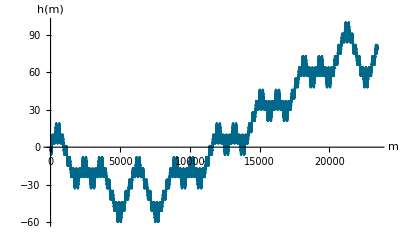

```mathematica
(* the height function *)
ListPlot[B3Heights,PlotRange->All,Filling->None,Joined->True,AxesLabel->{"m","h(m)"},PlotStyle->{BostonBlue}]
Export[NotebookDirectory[]<>"heightsB3.pdf",%];
```

```mathematica
mat=ho[ρ,B3Sub[10,"B"]];
{vals,vecs}=Eigensystem[mat];
o=Ordering[vals];
vals=vals[[o]];
vecs=vecs[[o]];
```

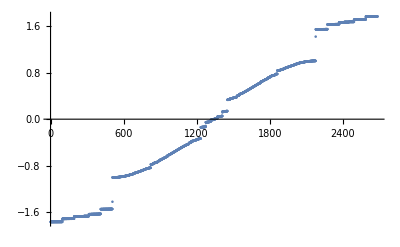

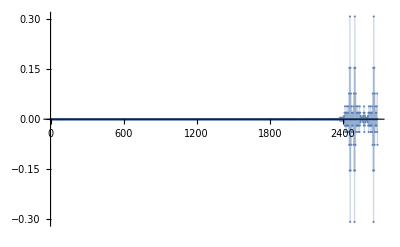

```mathematica
ListPlot[vals]
idxCenter=(Length[vals]+1)/2;
ListPlot[vecs[[idxCenter]],Filling->Axis,PlotRange->All]
```

```mathematica
(* the height function goes to 0 arbitrarily far from the origin *)
ρ=0.5;
ListPlot[ρ^B3Heights,Filling->Axis,PlotRange->All]
```

-Graphics-

```mathematica
B3Maxs=MaxHeights[B3Heights];
```

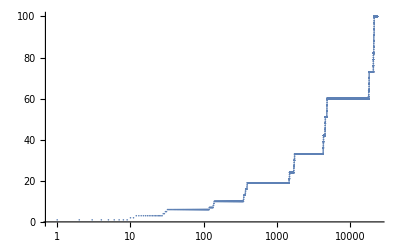

```mathematica
(* the height max doesn't grow logarithmically *)
ListLogLinearPlot[B3Maxs,PlotRange->All]
```

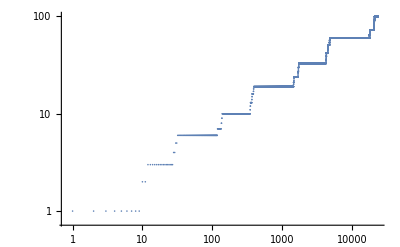

```mathematica
(* the height max grows like a power-law! *)
ListLogLogPlot[B3Maxs,PlotRange->All]
```

```mathematica
data=MapThread[{Log[#1],Log[#2]}&,{Range[Length[B3Maxs]],B3Maxs}];
```

0.113886+0.429665 x

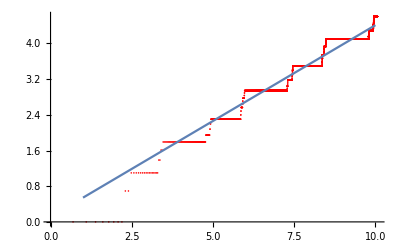

```mathematica
line=Fit [data,{1,x},x]
Show[ListPlot[data, PlotStyle->Red], Plot[line, {x, 1, 10}]]
```

```mathematica
(* chain substitution matrix *)
B3subM={{1,1},{3,0}};
Eigensystem[B3subM]
```

{{1/2 (1+√13),1/2 (1-√13)},{{1/6 (1+√13),1},{1/6 (1-√13),1}}}

```mathematica
(1/6 (1+√13))^-1//FullSimplify
%//N
```

1/2 (-1+√13)

1.30278

### Generalized inflation matrix

```mathematica
(* a dictionary from envs to indices *)
envs={"R","L","a","b"};
Idx=<|"R"->1,"L"->2,"a"->3,"b"->4|>;
inflatedEnvs=B3ArrowSub[1,#]&/@envs;
inflatedArrows=({0}~Join~B3Arrows2[#][[;;-2]])&/@inflatedEnvs;
inflatedHeights=Table[Total[#[[;;L]]],{L,1,Length[#]}]&/@inflatedArrows;
RowsHeights=MapThread[{#1,#2}&,{inflatedEnvs,inflatedHeights}];
(* construct the matrices *)
table0=Table[0,{i,1,4},{j,1,4}];
Clear[T];
(* number of relative height variations we consider *)
Htot=10;
T=Table[table0,{h,-Htot,Htot}];
(* a way of constructing the generalized matrices automatically *)
For[col=1,col≤4,col++,
{rows,heights}=RowsHeights[[col]];
rows=StringPartition[rows,1];
For[i=1,i≤Length[heights],i++,
h=heights[[i]];
row=Idx[rows[[i]]];
T[[Htot+1+h,col,row]]+=1;
]
]
```

```mathematica
Clear[Infl];
Infl[β_]:=β^-3 T[[Htot+1-3]]+β^-2 T[[Htot+1-2]]+β^-1 T[[Htot+1-1]]+T[[Htot+1]]+β^1 T[[Htot+1+1]]+β^2 T[[Htot+1+2]]+β^3 T[[Htot+1+3]]
```

```mathematica
Infl[β_]:=Total@Table[β^(idxH-Htot-1)T[[idxH]],{idxH,1,2Htot+1}]
```

```mathematica
sps=Table[Sort[Eigenvalues[Infl[β]]],{β,0.1,1.,0.01}];
```

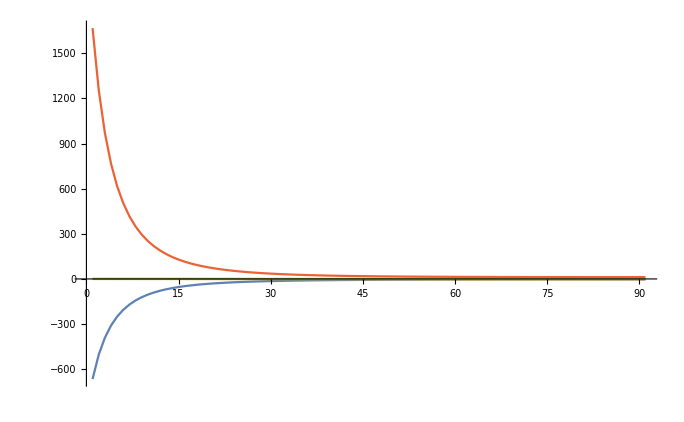

```mathematica
ListPlot[Transpose@sps,Joined->True,PlotRange->All]
```

```mathematica
Transpose[B3M]==Infl[1]
```

True

## Rudin-Shapiro substitution